```mathematica
SetDirectory["/home/krzysztof/Dropbox/Doktorat/Przekroje/Obrazki"];
lista=Import["LambdaDig.dat"];
lista2=Delete[lista,2]
```

{{2.55,0},{3.18751,205.727},{3.63264,318.54},{6.13359,1857.75}}

## Przekrój czynny Λ(1115)

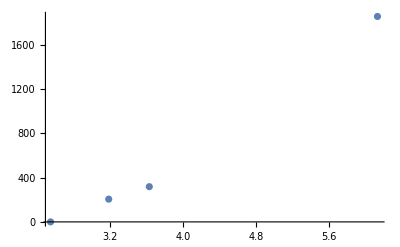

FittedModel[224.294 (-2.55+x)+81.999 (-2.55+x)^2]

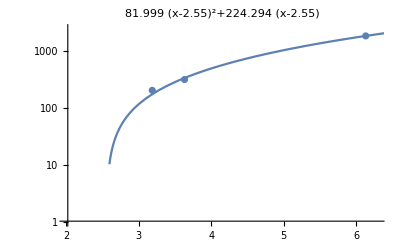

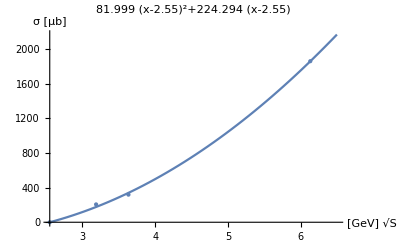

135.718

wykres1115Log.jpg

wykres1115.jpg

```mathematica
ListPlot[lista2, PlotRange->Full]
nlf1=NonlinearModelFit[lista2,a*(x-2.55)+b*(x-2.55)^2,{a,b},x]
lambda1115II=Show[
ListLogPlot[lista2, PlotRange->{{2,6.3},{1,2500}},PlotLabel->Normal[nlf1]],
LogPlot[nlf1[x],{x,2,6.5}]]
lambda1115I=Show[
Plot[nlf1[x],{x,2.55,6.5},AxesLabel->{Sqrt[S]"[GeV]","σ [μb]"},PlotLabel->Normal[nlf1]],
ListPlot[lista2, PlotRange->Full,PlotStyle->PointSize[Large]]
]
Print[nlf1[3.06]]
Export["wykres1115Log.jpg",lambda1115II]
Export["wykres1115.jpg",lambda1115I]
```

### przekrój Λ(1520)

135.718

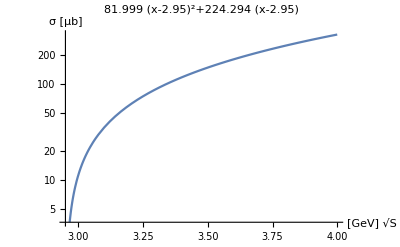

```mathematica
przek1520[s_]:=nlf1[2.55+(s-2.95)]
Print[przek1520[3.46]]
LogPlot[przek1520[x],{x,2.95,4},PlotLabel->Normal[przek1520[x]],AxesLabel->{Sqrt[S]"[GeV]","σ [μb]"}]
```

## Wydajność

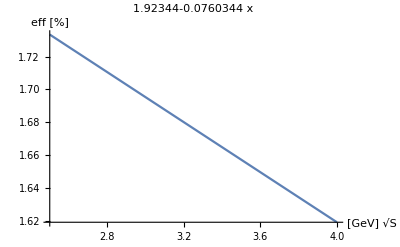

```mathematica
p1=-0.0760344;
p0=1.92344;
wydajnosc[s_]:=p1*s+p0;
Plot[wydajnosc[x],{x,2.5,4},PlotLabel->Normal[wydajnosc[x]],AxesLabel->{Sqrt[S]"[GeV]","eff [%]"}]
```

## Iloczyn

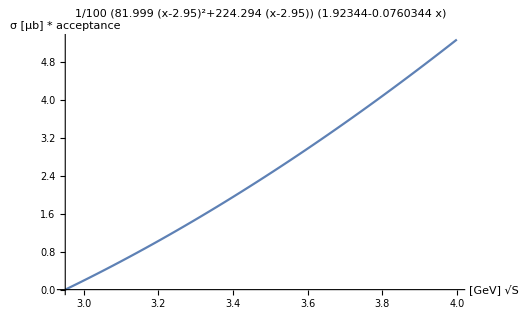

```mathematica
iloczyn[s_]:=przek1520[s]*wydajnosc[s]/100;
Plot[iloczyn[s],{s,2.95,4},AxesLabel->{Sqrt[S]"[GeV]","σ [μb] * acceptance"},PlotLabel->iloczyn[x]]
```